## Vector Fields

{2 x+3 y,4 x+y}

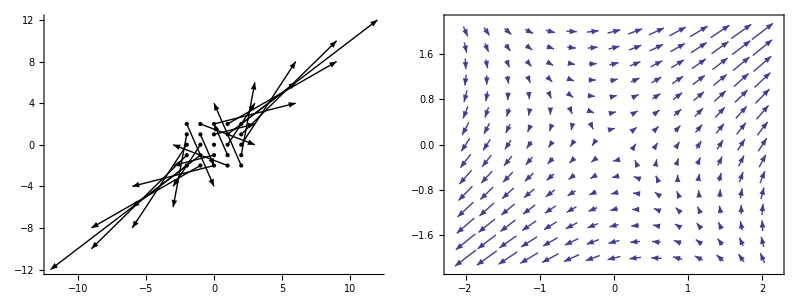

{{2,3},{4,1}}

{5,-2}

{{1,1},{-3,4}}

```mathematica
F={2x+3y,4x+1y}

xBounds={x, -2,2};
yBounds={y, -2,2};
arrows=Table[Arrow[{{x,y},{x,y}+F}],Evaluate[xBounds],Evaluate[yBounds]];
points=Table[Point[{x,y}],Evaluate[xBounds],Evaluate[yBounds]];
Grid[{{Graphics[Flatten[{arrows,PointSize[Medium],points}],Axes->True,ImageSize->Medium],
If[$VersionNumber<7,Needs["VectorFieldPlots`"];
VectorFieldPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium],
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium]]
}}]
DF=D[F,{{x,y}}]
Eigenvalues[DF]
Eigenvectors[DF]
Clear[x,y,F,xBounds,yBounds]
```

{-y,x}

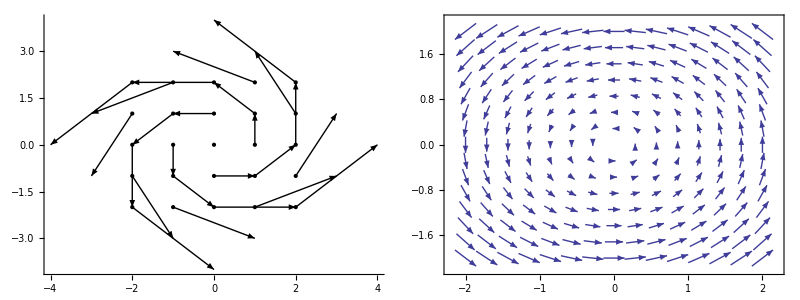

{{0,-1},{1,0}}

{ⅈ,-ⅈ}

{{ⅈ,1},{-ⅈ,1}}

```mathematica
F={-y,x}

xBounds={x, -2,2};
yBounds={y, -2,2};
arrows=Table[Arrow[{{x,y},{x,y}+F}],Evaluate[xBounds],Evaluate[yBounds]];
points=Table[Point[{x,y}],Evaluate[xBounds],Evaluate[yBounds]];
Grid[{{Graphics[Flatten[{arrows,PointSize[Medium],points}],Axes->True,ImageSize->Medium],
If[$VersionNumber<7,Needs["VectorFieldPlots`"];
VectorFieldPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium],
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium]]
}}]
DF=D[F,{{x,y}}]
Eigenvalues[DF]
Eigenvectors[DF]
Clear[x,y,F,xBounds,yBounds]
```

{2 x+y,x+2 y}

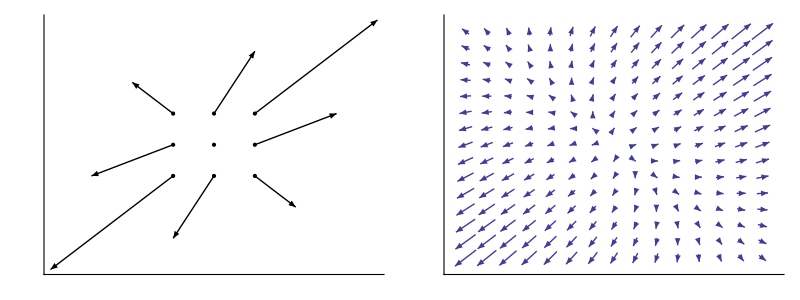

{{2,1},{1,2}}

{3,1}

{{1,1},{-1,1}}

```mathematica
F={2x+y,x+2y}

xBounds={x, -1,1};
yBounds={y, -1,1};
arrows=Table[Arrow[{{x,y},{x,y}+F}],Evaluate[xBounds],Evaluate[yBounds]];
points=Table[Point[{x,y}],Evaluate[xBounds],Evaluate[yBounds]];
Grid[{{Graphics[Flatten[{arrows,PointSize[Medium],points}],Ticks->None,Axes->True,Frame->False,ImageSize->Medium],
If[$VersionNumber<7,Needs["VectorFieldPlots`"];
VectorFieldPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium],
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium]]
}}]
DF=D[F,{{x,y}}]
Eigenvalues[DF]
Eigenvectors[DF]
Clear[x,y,F,xBounds,yBounds]
```

{{2,1},{1,2}}

{2 x+y,x+2 y}

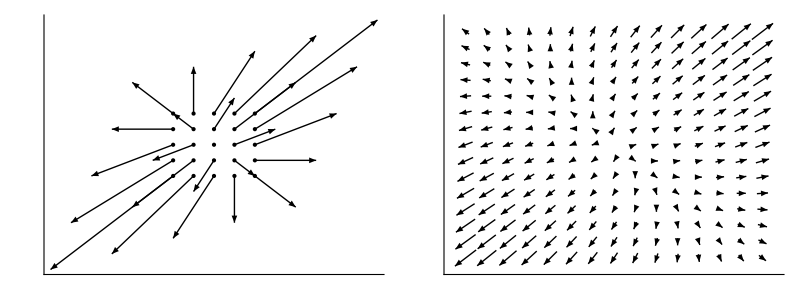

{{2,1},{1,2}}

{3,1}

{{1,1},{-1,1}}

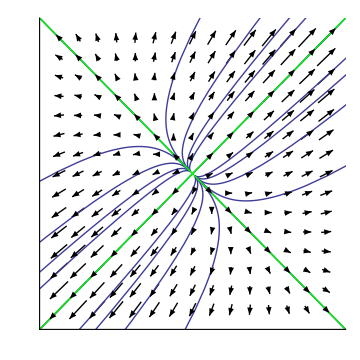

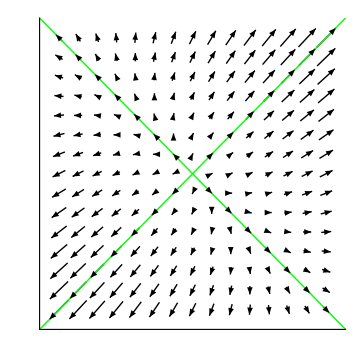

{{ⅇ^(2 t),ⅇ^t},{ⅇ^t,ⅇ^(2 t)}}

```mathematica
A=({{2, 1}, {1, 2}})

F=A.{x,y}

xBounds={x, -2,2};
yBounds={y, -2,2};
arrows=Table[Arrow[{{x,y},{x,y}+F}],Evaluate[xBounds],Evaluate[yBounds]];
points=Table[Point[{x,y}],Evaluate[xBounds],Evaluate[yBounds]];
Grid[{{Graphics[Flatten[{arrows,PointSize[Medium],points}],Ticks->None,Axes->True,Frame->False,ImageSize->Medium],
If[$VersionNumber<7,Needs["VectorFieldPlots`"];
VectorFieldPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium],
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black]]
}}]
DF=D[F,{{x,y}}]
Eigenvalues[DF]
EV=Eigenvectors[DF]
xBounds={x, -10,10};
yBounds={y, -10,10};
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black],
Table[Table[ParametricPlot[MatrixExp[A*t].{j,k},{t,-2,2},PlotStyle->Thick],{k,-4,4,2}],{j,-4,4,2}],
ParametricPlot[{EV[[1]]*t,EV[[2]]*t},{t,-20,20},PlotStyle->{{Thick,Green}}]
]
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black],
ParametricPlot[{EV[[1]]*t,EV[[2]]*t},{t,-20,20},PlotStyle->{{Thick,Green}}]
]
Exp[A*t]
Clear[x,y,F,xBounds,yBounds]
```

```mathematica
MatrixExp[A*t]
```

{{1/2 ⅇ^t (1+ⅇ^(2 t)),1/2 ⅇ^t (-1+ⅇ^(2 t))},{1/2 ⅇ^t (-1+ⅇ^(2 t)),1/2 ⅇ^t (1+ⅇ^(2 t))}}

{{2 t,t},{t,2 t}}

{{0,-1},{1,0}}

{-y,x}

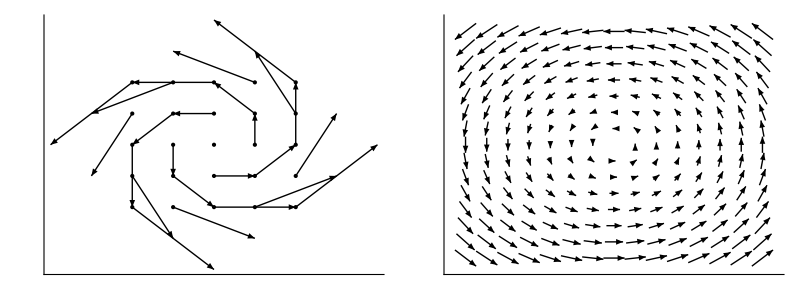

{{0,-1},{1,0}}

{ⅈ,-ⅈ}

{{ⅈ,1},{-ⅈ,1}}

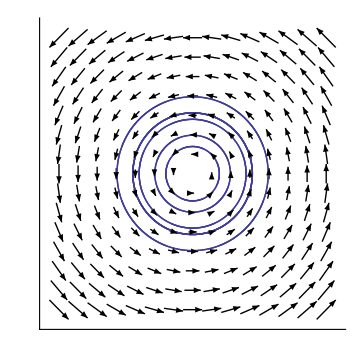

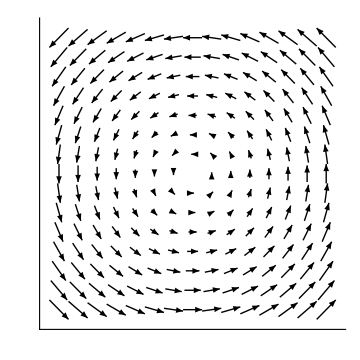

{{1,ⅇ^-t},{ⅇ^t,1}}

```mathematica
A=({{0, -1}, {1, 0}})

F=A.{x,y}

xBounds={x, -2,2};
yBounds={y, -2,2};
arrows=Table[Arrow[{{x,y},{x,y}+F}],Evaluate[xBounds],Evaluate[yBounds]];
points=Table[Point[{x,y}],Evaluate[xBounds],Evaluate[yBounds]];
Grid[{{Graphics[Flatten[{arrows,PointSize[Medium],points}],Ticks->None,Axes->True,Frame->False,ImageSize->Medium],
If[$VersionNumber<7,Needs["VectorFieldPlots`"];
VectorFieldPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium],
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black]]
}}]
DF=D[F,{{x,y}}]
Eigenvalues[DF]
EV=Eigenvectors[DF]
xBounds={x, -10,10};
yBounds={y, -10,10};
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black],
Table[Table[ParametricPlot[MatrixExp[A*t].{j,k},{t,-2,2},PlotStyle->Thick],{k,-4,4,2}],{j,-4,4,2}]
]
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black]
]
Exp[A*t]
Clear[x,y,F,xBounds,yBounds]
```

{{1,4},{2,3}}

{x+4 y,2 x+3 y}

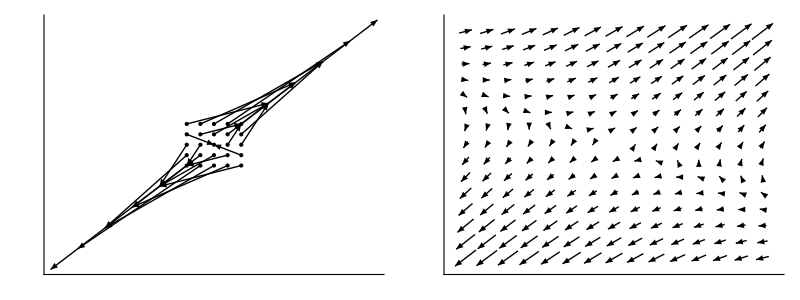

{{1,4},{2,3}}

{5,-1}

{{1,1},{-2,1}}

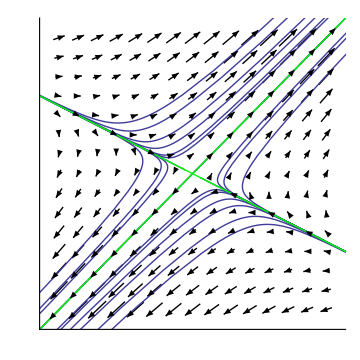

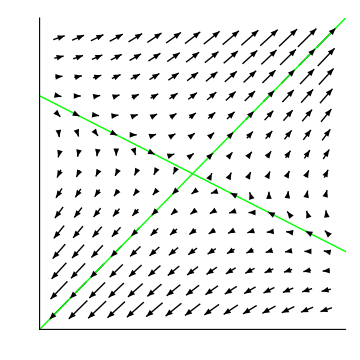

{{ⅇ^t,ⅇ^(4 t)},{ⅇ^(2 t),ⅇ^(3 t)}}

```mathematica
A=({{1, 4}, {2, 3}})

F=A.{x,y}

xBounds={x, -2,2};
yBounds={y, -2,2};
arrows=Table[Arrow[{{x,y},{x,y}+F}],Evaluate[xBounds],Evaluate[yBounds]];
points=Table[Point[{x,y}],Evaluate[xBounds],Evaluate[yBounds]];
Grid[{{Graphics[Flatten[{arrows,PointSize[Medium],points}],Ticks->None,Axes->True,Frame->False,ImageSize->Medium],
If[$VersionNumber<7,Needs["VectorFieldPlots`"];
VectorFieldPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium],
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black]]
}}]
DF=D[F,{{x,y}}]
Eigenvalues[DF]
EV=Eigenvectors[DF]
xBounds={x, -10,10};
yBounds={y, -10,10};
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black],
Table[Table[ParametricPlot[MatrixExp[A*t].{j,k},{t,-2,2},PlotStyle->Thick],{k,-4,4,2}],{j,-4,4,2}],
ParametricPlot[{EV[[1]]*t,EV[[2]]*t},{t,-20,20},PlotStyle->{{Thick,Green}}]
]
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black],
ParametricPlot[{EV[[1]]*t,EV[[2]]*t},{t,-20,20},PlotStyle->{{Thick,Green}}]
]
Exp[A*t]
Clear[x,y,F,xBounds,yBounds]
```

{{1,-1},{1,1}}

{x-y,x+y}

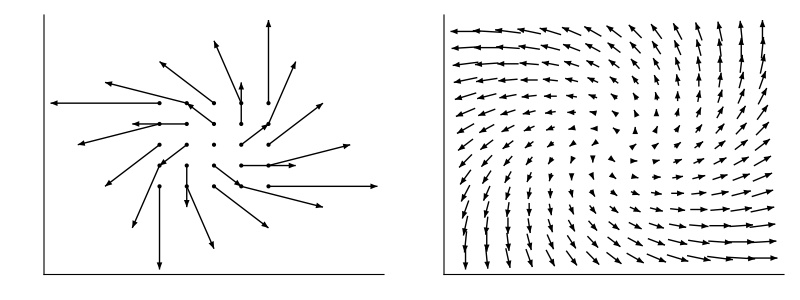

{{1,-1},{1,1}}

{1+ⅈ,1-ⅈ}

{{ⅈ,1},{-ⅈ,1}}

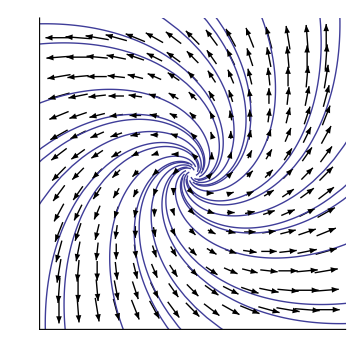

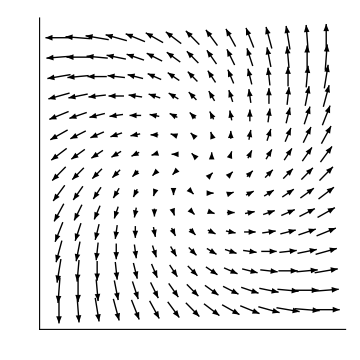

{{ⅇ^t,ⅇ^-t},{ⅇ^t,ⅇ^t}}

```mathematica
A=({{1, -1}, {1, 1}})

F=A.{x,y}

xBounds={x, -2,2};
yBounds={y, -2,2};
arrows=Table[Arrow[{{x,y},{x,y}+F}],Evaluate[xBounds],Evaluate[yBounds]];
points=Table[Point[{x,y}],Evaluate[xBounds],Evaluate[yBounds]];
Grid[{{Graphics[Flatten[{arrows,PointSize[Medium],points}],Ticks->None,Axes->True,Frame->False,ImageSize->Medium],
If[$VersionNumber<7,Needs["VectorFieldPlots`"];
VectorFieldPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium],
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black]]
}}]
DF=D[F,{{x,y}}]
Eigenvalues[DF]
EV=Eigenvectors[DF]
xBounds={x, -10,10};
yBounds={y, -10,10};
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black],
Table[Table[ParametricPlot[MatrixExp[A*t].{j,k},{t,-2,2},PlotStyle->Thick],{k,-4,4,2}],{j,-4,4,2}]
]
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black]
]
Exp[A*t]
Clear[x,y,F,xBounds,yBounds]
```

{{-2,1},{1,-2}}

{-2 x+y,x-2 y}

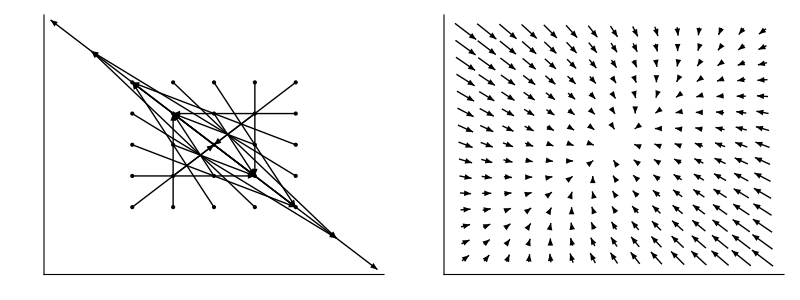

{{-2,1},{1,-2}}

{-3,-1}

{{-1,1},{1,1}}

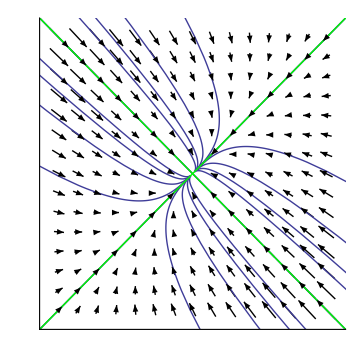

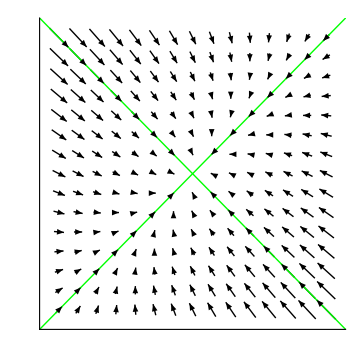

{{ⅇ^(-2 t),ⅇ^t},{ⅇ^t,ⅇ^(-2 t)}}

```mathematica
A=({{-2, 1}, {1, -2}})

F=A.{x,y}

xBounds={x, -2,2};
yBounds={y, -2,2};
arrows=Table[Arrow[{{x,y},{x,y}+F}],Evaluate[xBounds],Evaluate[yBounds]];
points=Table[Point[{x,y}],Evaluate[xBounds],Evaluate[yBounds]];
Grid[{{Graphics[Flatten[{arrows,PointSize[Medium],points}],Ticks->None,Axes->True,Frame->False,ImageSize->Medium],
If[$VersionNumber<7,Needs["VectorFieldPlots`"];
VectorFieldPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Frame->True,Axes->True,ImageSize->Medium],
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black]]
}}]
DF=D[F,{{x,y}}]
Eigenvalues[DF]
EV=Eigenvectors[DF]
xBounds={x, -10,10};
yBounds={y, -10,10};
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black],
Table[Table[ParametricPlot[MatrixExp[A*t].{j,k},{t,-2,2},PlotStyle->Thick],{k,-4,4,2}],{j,-4,4,2}],
ParametricPlot[{EV[[1]]*t,EV[[2]]*t},{t,-20,20},PlotStyle->{{Thick,Green}}]
]
Show[
VectorPlot[Evaluate[F], Evaluate[xBounds], Evaluate[yBounds],Ticks->None,Axes->True,Frame->False,ImageSize->Medium,VectorStyle->Black],
ParametricPlot[{EV[[1]]*t,EV[[2]]*t},{t,-20,20},PlotStyle->{{Thick,Green}}]
]
Exp[A*t]
Clear[x,y,F,xBounds,yBounds]
```

## Projections

```mathematica
u={1,1,1}
v={0,2,4}
b={1,3,6}
w=5/6u+5/4v
n=b-w
b=w+10n
z={0,0,0}
```

{1,1,1}

{0,2,4}

{1,3,6}

{5/6,10/3,35/6}

{1/6,-1/3,1/6}

{5/2,0,15/2}

{0,0,0}

```mathematica
Show[
Graphics3D[{
Arrow[{z,u}],Arrow[{z,v}],Arrow[{z,b}],Arrow[{z,w}],Arrow[{w,b}]
},Boxed->False],
ParametricPlot3D[t u + s v,{t,0,5/6},{s,0, 5/4},PlotStyle->{Black,Opacity[.1]},Mesh->None]
]
```

-Graphics3D-

## Column Space

```mathematica
A=({{2, 3, 1}, {-3, -5, 3}})
Grid[({{"A", A}, {"R=A.rref", R=A//RowReduce}, {"A^T", AT=A//Transpose}, {"rref(A^T)", RT=AT//RowReduce}}),Frame->All]
A//TeXForm
Grid[({{"vector", "Coordinates"}, {v={2,1}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}, {v={-1,3}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}}),Frame->All]
Grid[{NullSpace[A],NullSpace[AT]}]
```

{{2,3,1},{-3,-5,3}}

A | {{2,3,1},{-3,-5,3}}
R=A.rref | {{1,0,14},{0,1,-9}}
A^T | {{2,-3},{3,-5},{1,3}}
rref(A^T) | {{1,0},{0,1},{0,0}}

vector | Coordinates
{2,1} | {13,-8}
{-1,3} | {4,-3}

{-14,9,1}

\left(
\begin{array}{ccc}
 2 & 3 & 1 \\
 -3 & -5 & 3
\end{array}
\right)

```mathematica
A=({{2, 4, 1}, {1, 2, 3}})
Grid[({{"A", A}, {"R=A.rref", R=A//RowReduce}, {"A^T", AT=A//Transpose}, {"rref(A^T)", RT=AT//RowReduce}}),Frame->All]
Grid[({{"vector", "Coordinates"}, {v={6,3}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}, {v={-1,3}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}}),Frame->All]
A//TeXForm
Grid[{NullSpace[A],NullSpace[AT]}]
```

{{2,4,1},{1,2,3}}

A | {{2,4,1},{1,2,3}}
R=A.rref | {{1,2,0},{0,0,1}}
A^T | {{2,1},{4,2},{1,3}}
rref(A^T) | {{1,0},{0,1},{0,0}}

vector | Coordinates
{6,3} | {3,0}
{-1,3} | {-6/5,7/5}

{-2,1,0}

\left(
\begin{array}{ccc}
 2 & 4 & 1 \\
 1 & 2 & 3
\end{array}
\right)

```mathematica
A=({{1, 2, 3}, {2, 0, 1}, {-3, -2, -4}})
Grid[({{"A", A}, {"R=A.rref", R=A//RowReduce}, {"A^T", AT=A//Transpose}, {"rref(A^T)", RT=AT//RowReduce}}),Frame->All]
Grid[({{"vector", "Coordinates"}, {v=A.{-3,0,2}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}, {v={-1,3,2}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}}),Frame->All]
A//TeXForm
Grid[{NullSpace[A],NullSpace[Transpose[A]]}]
```

{{1,2,3},{2,0,1},{-3,-2,-4}}

A | {{1,2,3},{2,0,1},{-3,-2,-4}}
R=A.rref | {{1,0,1/2},{0,1,5/4},{0,0,0}}
A^T | {{1,2,-3},{2,0,-2},{3,1,-4}}
rref(A^T) | {{1,0,-1},{0,1,-1},{0,0,0}}

vector | Coordinates
{3,-4,1} | {-2,5/2,0}
{-1,3,2} | {0,0,1}

{-2,-5,4}
{1,1,1}

\left(
\begin{array}{ccc}
 1 & 2 & 3 \\
 2 & 0 & 1 \\
 -3 & -2 & -4
\end{array}
\right)

```mathematica
A=({{1, 3, 2}, {2, 1, 0}, {-3, -4, -2}})
Grid[({{"A", A}, {"R=A.rref", R=A//RowReduce}, {"A^T", AT=A//Transpose}, {"rref(A^T)", RT=AT//RowReduce}}),Frame->All]
Grid[({{"vector", "Coordinates"}, {v=A.{-3,2,0}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}, {v=A.{-2,1,1}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}}),Frame->All]
A//TeXForm
Grid[{NullSpace[A],NullSpace[Transpose[A]]}]
```

{{1,3,2},{2,1,0},{-3,-4,-2}}

A | {{1,3,2},{2,1,0},{-3,-4,-2}}
R=A.rref | {{1,0,-2/5},{0,1,4/5},{0,0,0}}
A^T | {{1,2,-3},{3,1,-4},{2,0,-2}}
rref(A^T) | {{1,0,-1},{0,1,-1},{0,0,0}}

vector | Coordinates
{3,-4,1} | {-3,2,0}
{3,-3,0} | {-12/5,9/5,0}

{2,-4,5}
{1,1,1}

\left(
\begin{array}{ccc}
 1 & 3 & 2 \\
 2 & 1 & 0 \\
 -3 & -4 & -2
\end{array}
\right)

```mathematica
A=({{2, 1, -2, 4}, {1, 3, 0, 5}, {-2, 1, 1, 2}})
Grid[({{"A", A}, {"R=A.rref", R=A//RowReduce}, {"A^T", AT=A//Transpose}, {"rref(A^T)", RT=AT//RowReduce}}),Frame->All]
Grid[({{"vector", "Coordinates"}, {v=A.{-3,2,0,1}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}, {v=A.{-2,1,1,-2}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}}),Frame->All]
A//TeXForm
Grid[{NullSpace[A],NullSpace[Transpose[A]]}]
```

{{2,1,-2,4},{1,3,0,5},{-2,1,1,2}}

A | {{2,1,-2,4},{1,3,0,5},{-2,1,1,2}}
R=A.rref | {{1,0,0,-1},{0,1,0,2},{0,0,1,-2}}
A^T | {{2,1,-2},{1,3,1},{-2,0,1},{4,5,2}}
rref(A^T) | {{1,0,0},{0,1,0},{0,0,1},{0,0,0}}

vector | Coordinates
{0,8,10} | {-4,4,-2}
{-13,-9,2} | {0,-3,5}

{1,-2,2,1}

\left(
\begin{array}{cccc}
 2 & 1 & -2 & 4 \\
 1 & 3 & 0 & 5 \\
 -2 & 1 & 1 & 2
\end{array}
\right)

```mathematica
A=({{0, 1, 2, 3}, {2, -1, -4, 0}, {-1, 2, 5, 5}})
Grid[({{"A", A}, {"R=A.rref", R=A//RowReduce}, {"A^T", AT=A//Transpose}, {"rref(A^T)", RT=AT//RowReduce}}),Frame->All]
Grid[({{"vector", "Coordinates"}, {v=A.{1,2,0,-3}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}, {v=A.{-1,3,-4,-1}, (Append[AT,v]//Transpose//RowReduce//Transpose)[[-1]]}}),Frame->All]
A//TeXForm
Grid[{NullSpace[A],NullSpace[Transpose[A]]}]
```

{{0,1,2,3},{2,-1,-4,0},{-1,2,5,5}}

A | {{0,1,2,3},{2,-1,-4,0},{-1,2,5,5}}
R=A.rref | {{1,0,-1,0},{0,1,2,0},{0,0,0,1}}
A^T | {{0,2,-1},{1,-1,2},{2,-4,5},{3,0,5}}
rref(A^T) | {{1,0,0},{0,1,0},{0,0,1},{0,0,0}}

vector | Coordinates
{-7,0,-12} | {1,2,-3}
{-8,11,-18} | {3,-5,-1}

{1,-2,1,0}

\left(
\begin{array}{cccc}
 0 & 1 & 2 & 3 \\
 2 & -1 & -4 & 0 \\
 -1 & 2 & 5 & 5
\end{array}
\right)

## Null Space, EigenSpace, Orthogonal Complement

```mathematica
u={0,3,-1}
v={-2,1,0}
A={3u,2v,2v-u}//Transpose
A//RowReduce
NullSpace[A]
A//Transpose//RowReduce
NullSpace[A//Transpose]
TeXForm[A]
```

{0,3,-1}

{-2,1,0}

{{0,-4,-4},{9,2,-1},{-3,0,1}}

{{1,0,-1/3},{0,1,1},{0,0,0}}

{{1,-3,3}}

{{1,0,-1/6},{0,1,-1/3},{0,0,0}}

{{1,2,6}}

\left(
\begin{array}{ccc}
 0 & -4 & -4 \\
 9 & 2 & -1 \\
 -3 & 0 & 1
\end{array}
\right)

```mathematica
u={2,3,-1,0}
v={-1,2,0,4}
A={u,2u,2v-u,-2u+3v}//Transpose
A//RowReduce
NullSpace[A]
NullSpace[A//Transpose]
TeXForm[A]
```

{2,3,-1,0}

{-1,2,0,4}

{{2,4,-4,-7},{3,6,1,0},{-1,-2,1,2},{0,0,8,12}}

{{1,2,0,-1/2},{0,0,1,3/2},{0,0,0,0},{0,0,0,0}}

{{1,0,-3,2},{-2,1,0,0}}

{{12,-8,0,7},{2,1,7,0}}

\left(
\begin{array}{cccc}
 2 & 4 & -4 & -7 \\
 3 & 6 & 1 & 0 \\
 -1 & -2 & 1 & 2 \\
 0 & 0 & 8 & 12
\end{array}
\right)

```mathematica
u={2,-1,2}
v={0,3,1}
A={u,-2v,v+2u,u-v}//Transpose
A//RowReduce
NullSpace[A]
A//Transpose//RowReduce
NullSpace[A//Transpose]
TeXForm[A]
```

{2,-1,2}

{0,3,1}

{{2,0,4,2},{-1,-6,1,-4},{2,-2,5,1}}

{{1,0,2,1},{0,1,-1/2,1/2},{0,0,0,0}}

{{-2,-1,0,2},{-4,1,2,0}}

{{1,0,7/6},{0,1,1/3},{0,0,0},{0,0,0}}

{{-7,-2,6}}

\left(
\begin{array}{cccc}
 2 & 0 & 4 & 2 \\
 -1 & -6 & 1 & -4 \\
 2 & -2 & 5 & 1
\end{array}
\right)

```mathematica
u={2,-1,2,0}
v={0,3,1,-2}
A={v,2u,-v+2u}//Transpose
A//RowReduce
NullSpace[A]
A//Transpose//RowReduce
NullSpace[A//Transpose]
TeXForm[A]
```

{2,-1,2,0}

{0,3,1,-2}

{{0,4,4},{3,-2,-5},{1,4,3},{-2,0,2}}

{{1,0,-1},{0,1,1},{0,0,0},{0,0,0}}

{{1,-1,1}}

{{1,0,7/6,-1/3},{0,1,1/3,-2/3},{0,0,0,0}}

{{1,2,0,3},{-7,-2,6,0}}

\left(
\begin{array}{ccc}
 0 & 4 & 4 \\
 3 & -2 & -5 \\
 1 & 4 & 3 \\
 -2 & 0 & 2
\end{array}
\right)

```mathematica
d=({{3, 0, 0}, {0, 3, 1}, {0, 0, 3}})
Q=({{2, 1, 3}, {0, 1, -2}, {2, 2, 2}})
A=Q.d.Inverse[Q]
Eigenvalues[A]
Eigenvectors[A]
TeXForm[A]
```

{{3,0,0},{0,3,1},{0,0,3}}

{{2,1,3},{0,1,-2},{2,2,2}}

{{2,-1,1},{-1,2,1},{-2,-2,5}}

{3,3,3}

{{1,0,1},{-1,1,0},{0,0,0}}

\left(
\begin{array}{ccc}
 2 & -1 & 1 \\
 -1 & 2 & 1 \\
 -2 & -2 & 5
\end{array}
\right)

```mathematica
d=({{2, 0, 0}, {0, 2, 1}, {0, 0, 2}})
Q=({{1, 2, 2}, {0, 3, 1}, {1, -2, 1}})
A=Q.d.Inverse[Q]
Eigenvalues[A]
Eigenvectors[A]
TeXForm[A]
```

{{2,0,0},{0,2,1},{0,0,2}}

{{1,2,2},{0,3,1},{1,-2,1}}

{{-4,8,6},{-9,14,9},{6,-8,-4}}

{2,2,2}

{{1,0,1},{4,3,0},{0,0,0}}

\left(
\begin{array}{ccc}
 -4 & 8 & 6 \\
 -9 & 14 & 9 \\
 6 & -8 & -4
\end{array}
\right)